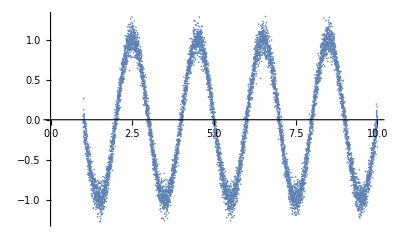

```mathematica
tab=Table[{λ,Sin[2π λ/2]+RandomReal[NormalDistribution[0,0.1]]},{λ,1,10,0.001}];
ListPlot[tab]
```

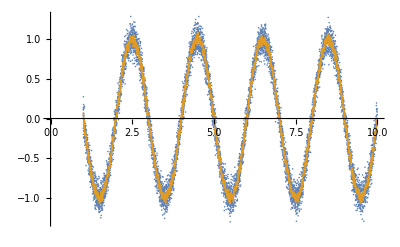

```mathematica
ListPlot[{tab,MovingAverage[tab,10]}]
```

### Normal binning

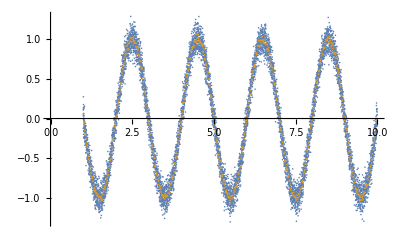

```mathematica
bin=10;
j=0;Label[jloop];j=j+1;Subscript[binpoint, j]=Mean[tab[[1+(j-1)bin;;j bin]]];If[j<Floor[Length[tab]/bin],Goto[jloop]];
binneddata=Table[Subscript[binpoint, j],{j,1,Floor[Length[tab]/bin]}];
ListPlot[{tab,binneddata}]
```

```mathematica
Length[tab[[1;;10]]]
Length[tab[[11;;20]]]
...
Length[tab[[1+(j-1)bin;;j bin]]]
```

10

10

### Normal smoothing

```mathematica
bin=10;
j=0;Label[jloop];j=j+1;Subscript[smoothpoint, j]=Mean[tab[[1+(j-1);;(j-1)+bin]]];If[j<Length[tab]-bin+1,Goto[jloop]];
smootheddata=Table[Subscript[smoothpoint, j],{j,1,Length[tab]-bin+1}];
ListPlot[{tab,smootheddata}]
```

-Graphics-

```mathematica
Length[tab[[1;;10]]]
Length[tab[[2;;11]]]
...
Length[tab[[1+(j-1);;(j-1)+bin]]]
```

10

10

```mathematica
(j-1)+bin==Length[tab]
j==Length[tab]-bin+1
```

### Adaptive smoothing

```mathematica
R=10;binλ[λ_]:=λ/R;
j=0;Label[jloop];j=j+1;testλ=tab[[j]][[1]];temp=Select[tab,testλ-binλ[testλ]/2<#[[1]]<testλ+binλ[testλ]/2&];Subscript[smoothpoint, j]=Mean[temp];If[j<Length[tab],Goto[jloop]];
```

```mathematica
NMinimize[{(Aoverlapcircles-Aoverlapreal)^2,0<p<1},p]
```

NMinimize::nrnum: The function value 0.887138-0.404404 ⅈ is not a real number at {p} = {0.0457318}.

NMinimize[{(-0.03509+(-1/2 √(3.57497-(1.89374-p^2)^2)+p^2 ArcCos[0.528888 (1.89374-p^2)]+ArcCos[(0.528888 (-0.106257+p^2))/p])/π)^2,0<p<1},p]